```mathematica
p=Polygon[{
{1,4,1},
{1,2,3},
{2,1,3},
{3,1,2},
{3,2,1}
}];
Graphics3D[{Orange,p},Axes->True,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
translate[{x_,y_,z_}]:=Block[
{m1},
m1=({{1, 0, x}, {0, 1, y}, {-1, -1, z-6}});
Return[{
m1[[1]][[3]],
m1[[2]][[3]]
}];
];
```

```mathematica
translate[{1,4,1}]
translate[{1,2,3}]
translate[{2,1,3}]
translate[{3,1,2}]
translate[{3,2,1}]
```

{1,4}

{1,2}

{2,1}

{3,1}

{3,2}

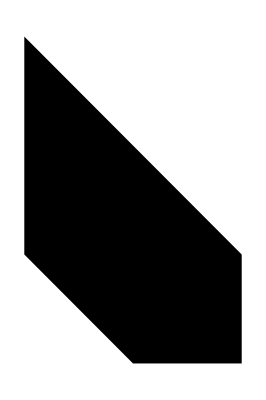

```mathematica
Graphics[Polygon[{
{1,4},
{1,2},
{2,1},
{3,1},
{3,2}
}]]
```